```mathematica
Import[new.txt]
```

Import::chtype: First argument new . txt is not a valid file, directory, or URL specification.

$Failed

```mathematica
Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

8,9
8,10
8,11
8,13
9,8
9,9
9,10
9,11
9,12
9,13
9,14
10,8
10,9
10,10
10,11
10,12
10,13
11,10
11,11

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt"]
```

8,9
8,10
8,11
8,13
9,8
9,9
9,10
9,11
9,12
9,13
9,14
10,8
10,9
10,10
10,11
10,12
10,13
11,10
11,11

```mathematica
ListPlot[data]
```

ListPlot::lpn: "8,9\n8,10\n8,11\n8,13\n9,8\n9,9\n9,10\n9,11\n9,12\n9,13\n9,14\n10,8\n10,9\n10,10\n10,11\n10,12\n10,13\n11,10\n11,11" is not a list of numbers or pairs of numbers.

ListPlot[8,9
8,10
8,11
8,13
9,8
9,9
9,10
9,11
9,12
9,13
9,14
10,8
10,9
10,10
10,11
10,12
10,13
11,10
11,11]

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt"]
```

{8,11}
{9,9}
{9,10}
{9,11}
{9,12}
{9,13}
{9,14}
{9,15}
{10,9}
{10,10}
{10,11}
{10,12}
{10,13}
{11,8}
{11,9}
{11,10}
{11,11}
{11,12}

```mathematica
ListPlot[data]
```

ListPlot::lpn: "{8,11}\n{9,9}\n{9,10}\n{9,11}\n{9,12}\n{9,13}\n{9,14}\n{9,15}\n{10,9}\n{10,10}\n{10,11}\n{10,12}\n{10,13}\n{11,8}\n{11,9}\n{11,10}\n{11,11}\n{11,12}" is not a list of numbers or pairs of numbers.

ListPlot[{8,11}
{9,9}
{9,10}
{9,11}
{9,12}
{9,13}
{9,14}
{9,15}
{10,9}
{10,10}
{10,11}
{10,12}
{10,13}
{11,8}
{11,9}
{11,10}
{11,11}
{11,12}]

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt"]
```

(8,8)
(8,9)
(8,10)
(9,7)
(9,8)
(9,9)
(9,10)
(9,11)
(9,12)
(9,13)
(9,14)
(10,7)
(10,8)
(10,9)
(10,10)
(10,11)
(11,9)
(11,10)
(11,11)
(11,12)

```mathematica
ListPlot[data]
```

ListPlot::lpn: "(8,8)\n(8,9)\n(8,10)\n(9,7)\n(9,8)\n(9,9)\n(9,10)\n(9,11)\n(9,12)\n(9,13)\n(9,14)\n(10,7)\n(10,8)\n(10,9)\n(10,10)\n(10,11)\n(11,9)\n(11,10)\n(11,11)\n(11,12)" is not a list of numbers or pairs of numbers.

ListPlot[(8,8)
(8,9)
(8,10)
(9,7)
(9,8)
(9,9)
(9,10)
(9,11)
(9,12)
(9,13)
(9,14)
(10,7)
(10,8)
(10,9)
(10,10)
(10,11)
(11,9)
(11,10)
(11,11)
(11,12)]

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

{{(8,8)},{(8,9)},{(8,10)},{(9,7)},{(9,8)},{(9,9)},{(9,10)},{(9,11)},{(9,12)},{(9,13)},{(9,14)},{(10,7)},{(10,8)},{(10,9)},{(10,10)},{(10,11)},{(11,9)},{(11,10)},{(11,11)},{(11,12)}}

```mathematica
ListPlot[data]
```

-Graphics-

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

{{8,11},{8,12},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{11,9},{11,10},{11,11},{12,10}}

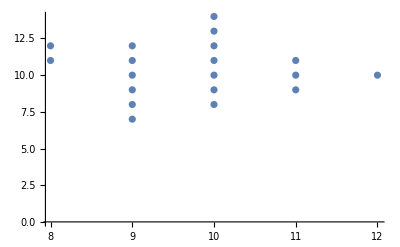

```mathematica
ListPlot[data]
```

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

{{11,15},{12,13},{12,14},{12,16},{12,17},{13,13},{13,14},{13,15},{13,16},{13,17},{13,18},{14,12},{14,14},{14,15},{14,17},{14,19},{15,14},{15,15},{15,16},{15,17},{15,18},{16,17},{16,18}}

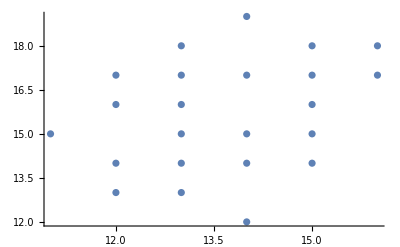

```mathematica
ListPlot[data]
```

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

{{142,156},{143,152},{143,153},{143,154},{143,155},{143,156},{143,157},{144,152},{144,153},{144,154},{145,149},{145,150},{145,151},{145,153},{145,154},{145,156},{146,147},{146,150},{146,151},{146,153},{146,154},{146,155},{147,146},{147,152},{147,153},{147,154},{148,145},{148,146},{148,147},{148,148},{148,149},{148,150},{148,151},{148,152},{148,153},{148,155},{148,156},{149,144},{149,145},{149,147},{149,150},{149,151},{149,152},{149,153},{149,154},{149,155},{149,156},{149,157},{149,158},{150,141},{150,142},{150,143},{150,145},{150,146},{150,150},{150,151},{150,152},{150,154},{150,155},{150,156},{150,157},{151,141},{151,142},{151,143},{151,144},{151,145},{151,148},{151,149},{151,153},{151,154},{151,155},{152,144},{152,145},{152,146},{152,148},{152,153},{152,154},{153,146},{153,147},{153,148},{153,150},{153,153},{154,143},{154,144},{154,145},{154,146},{154,147},{154,148},{155,145},{155,146},{155,147}}

```mathematica
data2 = Import["/home/s1220054/Dissertation/Dissertation/src/type2.txt", "CSV"]
```

{}

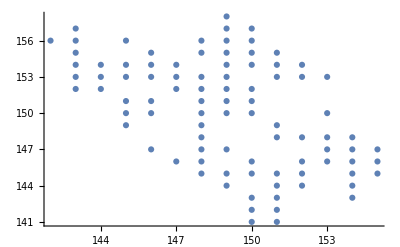

```mathematica
ListPlot[data]
```

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

{{143,149},{144,148},{144,149},{144,150},{144,151},{144,153},{144,154},{144,155},{145,146},{145,147},{145,148},{145,149},{145,150},{145,151},{145,152},{145,153},{145,154},{145,155},{145,156},{145,157},{146,143},{146,144},{146,145},{146,146},{146,147},{146,148},{146,149},{146,150},{146,151},{146,152},{146,153},{146,154},{146,155},{146,156},{146,157},{146,158},{147,143},{147,145},{147,146},{147,147},{147,148},{147,149},{147,150},{147,151},{147,152},{147,153},{147,154},{147,155},{147,156},{147,157},{148,142},{148,143},{148,144},{148,145},{148,146},{148,147},{148,148},{148,149},{148,150},{148,151},{148,152},{148,153},{148,154},{148,155},{148,156},{148,157},{149,141},{149,142},{149,143},{149,144},{149,145},{149,146},{149,147},{149,148},{149,149},{149,150},{149,151},{149,152},{149,153},{149,154},{149,155},{149,156},{149,157},{149,158},{150,140},{150,141},{150,142},{150,143},{150,144},{150,145},{150,146},{150,147},{150,148},{150,149},{150,150},{150,151},{150,152},{150,153},{150,154},{150,155},{150,156},{150,157},{150,158},{151,143},{151,144},{151,145},{151,146},{151,147},{151,148},{151,149},{151,150},{151,151},{151,152},{151,153},{151,154},{151,155},{151,156},{151,157},{152,144},{152,145},{152,146},{152,147},{152,148},{152,149},{152,150},{152,151},{152,152},{152,153},{152,154},{152,155},{152,156},{152,157},{152,158},{153,145},{153,146},{153,147},{153,148},{153,149},{153,150},{153,151},{153,152},{153,153},{153,154},{153,155},{153,156},{154,148},{154,149},{154,150}}

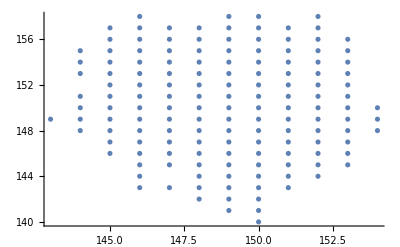

```mathematica
ListPlot[data]
```

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

{{144,148},{145,148},{145,151},{145,152},{145,153},{145,154},{146,147},{146,151},{146,155},{146,157},{146,158},{146,159},{146,160},{147,149},{147,150},{147,151},{147,152},{147,154},{147,155},{147,156},{147,157},{147,158},{147,159},{147,160},{148,144},{148,145},{148,147},{148,148},{148,150},{148,151},{148,153},{148,155},{148,156},{148,157},{148,158},{148,160},{149,143},{149,145},{149,146},{149,149},{149,151},{149,153},{149,154},{149,156},{149,157},{149,161},{150,143},{150,144},{150,145},{150,146},{150,147},{150,149},{150,150},{150,153},{150,154},{150,155},{150,156},{150,157},{150,158},{150,159},{150,160},{150,161},{151,143},{151,145},{151,151},{151,152},{151,153},{151,154},{151,155},{151,156},{151,157},{151,158},{151,160},{152,143},{152,144},{152,147},{152,151},{152,152},{152,153},{152,154},{152,156},{152,157},{152,158},{153,145}}

```mathematica
data2 = Import["/home/s1220054/Dissertation/Dissertation/src/type2.txt", "CSV"]
```

{{144,150},{144,151},{145,146},{145,147},{145,149},{145,150},{146,145},{146,146},{146,148},{146,149},{146,150},{146,152},{146,153},{146,154},{146,156},{147,142},{147,143},{147,144},{147,145},{147,146},{147,147},{147,148},{147,153},{148,142},{148,143},{148,146},{148,149},{148,152},{148,154},{148,159},{149,144},{149,147},{149,148},{149,150},{149,152},{149,155},{149,158},{149,159},{149,160},{150,148},{150,151},{150,152},{151,144},{151,146},{151,147},{151,148},{151,149},{151,150},{151,159},{152,145},{152,146},{152,148},{152,149},{152,150},{153,146},{153,148},{153,149},{153,150},{153,151},{153,152},{153,153},{154,148},{154,149},{154,150},{154,151},{154,152},{155,149},{155,150}}

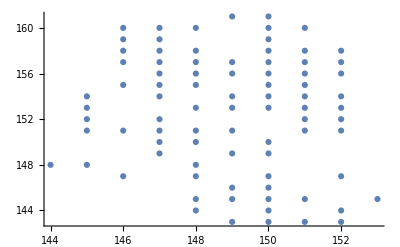

```mathematica
plot1 = ListPlot[data]
```

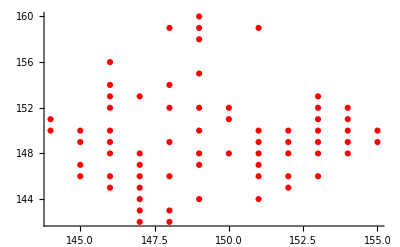

```mathematica
plot2 = ListPlot[data2, PlotStyle-> Red]
```

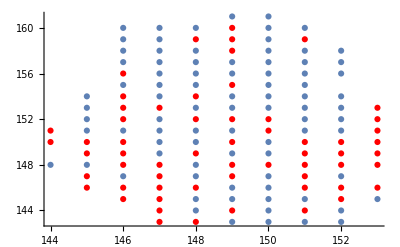

```mathematica
Show[plot1,plot2]
```

```mathematica
data2 = Import["/home/s1220054/Dissertation/Dissertation/src/type2.txt", "CSV"]
```

{{242,252},{243,252},{244,253},{244,256},{245,244},{245,250},{245,257},{246,244},{246,248},{246,251},{246,254},{246,258},{246,259},{246,261},{247,243},{247,250},{247,252},{247,253},{247,257},{247,259},{247,260},{247,261},{247,262},{248,244},{248,246},{248,252},{248,256},{248,257},{248,260},{248,262},{249,243},{249,244},{249,245},{249,249},{249,253},{249,254},{249,255},{249,256},{249,259},{249,260},{249,261},{249,262},{250,242},{250,243},{250,245},{250,252},{250,253},{250,255},{250,256},{250,258},{250,259},{250,260},{250,261},{251,244},{251,249},{251,251},{251,254},{251,256},{251,257},{251,258},{251,259},{251,260},{252,244},{252,245},{252,247},{252,250},{252,251},{252,257},{252,258},{252,259},{252,260},{252,261},{253,246},{253,249},{253,255},{253,260},{253,261},{254,248},{254,249},{254,252},{254,253},{254,256},{254,257},{255,250}}

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

{{241,255},{242,251},{242,253},{242,254},{242,255},{242,256},{243,250},{243,251},{243,253},{243,254},{243,255},{243,256},{243,257},{244,249},{244,250},{244,251},{244,252},{244,254},{244,255},{244,257},{244,258},{245,243},{245,245},{245,246},{245,247},{245,248},{245,249},{245,251},{245,252},{245,253},{245,254},{245,255},{245,256},{245,258},{245,259},{246,240},{246,241},{246,242},{246,243},{246,245},{246,246},{246,247},{246,249},{246,250},{246,252},{246,253},{246,255},{246,256},{246,257},{247,238},{247,239},{247,240},{247,241},{247,242},{247,244},{247,245},{247,246},{247,247},{247,248},{247,249},{247,251},{247,254},{247,255},{247,256},{247,258},{248,240},{248,241},{248,242},{248,243},{248,245},{248,247},{248,248},{248,249},{248,250},{248,251},{248,253},{248,254},{248,255},{248,258},{248,259},{248,261},{249,239},{249,240},{249,241},{249,242},{249,246},{249,247},{249,248},{249,250},{249,251},{249,252},{249,257},{249,258},{250,240},{250,241},{250,244},{250,246},{250,247},{250,248},{250,249},{250,250},{250,251},{250,254},{250,257},{251,240},{251,241},{251,242},{251,243},{251,245},{251,246},{251,247},{251,248},{251,250},{251,252},{251,253},{251,255},{252,242},{252,243},{252,246},{252,248},{252,249},{252,252},{252,253},{252,254},{252,255},{252,256},{253,244},{253,245},{253,247},{253,248},{253,250},{253,251},{253,252},{253,253},{253,254},{253,256},{253,257},{253,258},{253,259},{254,244},{254,245},{254,246},{254,247},{254,250},{254,251},{254,254},{254,255},{254,258},{254,259},{254,260},{255,245},{255,246},{255,247},{255,248},{255,249},{255,251},{255,252},{255,253},{255,254},{255,255},{255,256},{255,257},{255,258},{256,247},{256,249},{256,250},{256,251},{256,253}}

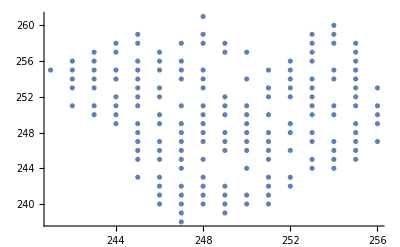

```mathematica
plot1 = ListPlot[data]
```

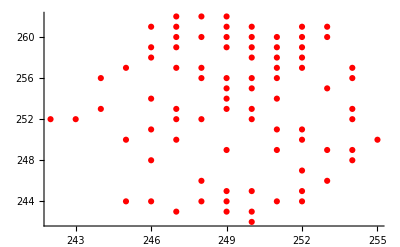

```mathematica
plot2 = ListPlot[data2, PlotStyle->Red]
```

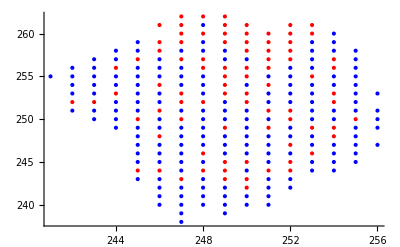

```mathematica
ListPlot[{data,data2},PlotStyle-> {Blue ,Red}]
```

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

{{259,295},{259,296},{259,297},{260,292},{260,293},{260,294},{260,295},{260,296},{260,297},{260,298},{260,299},{260,301},{261,291},3312,{338,309},{338,310},{338,318},{339,298},{339,306},{339,307},{339,308},{339,309},{339,310},{340,307},{340,309},{340,310}}
 |  |  |  |

```mathematica
data2 = Import["/home/s1220054/Dissertation/Dissertation/src/type2.txt", "CSV"]
```

{{257,311},{258,307},{258,308},{258,309},{258,310},{258,311},{258,312},{258,313},{259,305},{259,306},{259,307},{259,308},{259,309},4050,{339,312},{339,316},{339,317},{340,290},{340,291},{340,302},{340,303},{340,304},{340,305},{340,306},{340,308},{341,305}}
 |  |  |  |

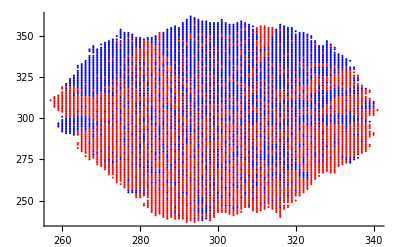

Show::gtype: Out is not a type of graphics.

```mathematica
ListPlot[{data,data2},PlotStyle-> {Blue ,Red}]
```